3.3333

General::munfl: 2.79355×10^-85 6.93143×10^-225 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 2.79355×10^-85 1.72183×10^-224 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 2.79355×10^-85 3.68525×10^-226 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

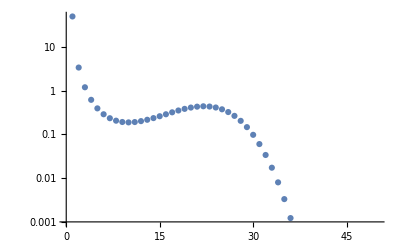

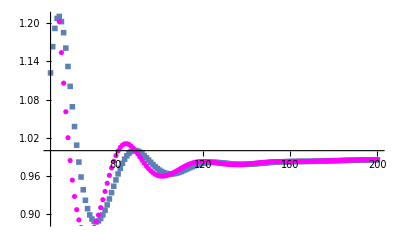

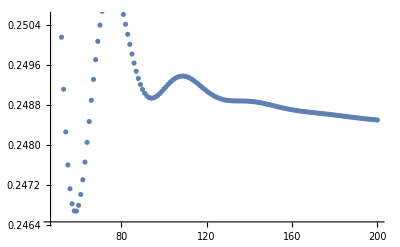

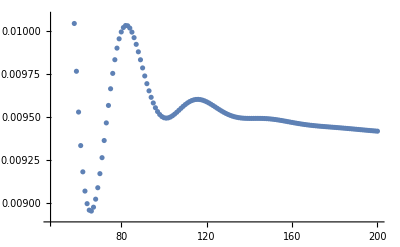

```mathematica
(* Mathematica notebook provided as supporting info for "Theory for chemical equilibrium in small systems: General results and examination of micelle self-assembly"
Olivia Beckwith,Robert Schneider,Lara Patel,Xiaokun Zhang,and James T.Kindt  (referred to hereafter as Beckwith 2023)
*)
(* Implementing calculations described in J. Chem.Theory Comput.2017, v 13,5195-5206 by Zhang et al.  (referred to hereafter as Zhang 2017) 
    eqs. 14-18 to calculate mean number m_j of clusters containing j monomers at a total monomer concentration Cfac as a function of the total number of monomers in the system Nsys*)
ClearAll;



PairsKratioModel= {};
PairsKratio={};

Unimers={};
jmers={};

Kactual= {};

(* Set parameters for free energy model *)
c1 = 4;
c2 = 1.5;
c3 = 0.000009;
c4 = 4;

(* Define free energy function *)
Fj[j_]:=c1*(j-1)^(2/3)-c2*(j-1)+c3*(j-1)^c4;

Nqs=50;  (* set number of cluster sizes*)
(* Calculate equilibrium constants *)

For [j=1,j ⩽ Nqs, j++,

             AppendTo  [Kactual,{j,N[ⅇ^(-Fj[j]) ]  }]
             
]

(* set size of cluster to analyze and plot *)
j = 10;  
Cfac = 3.3333    (* total monomer concentration *)
(* loop over systems of increasing size *)
For [Nsys= 50,Nsys < 201,Nsys++,

Volumefac = Nsys/Cfac;

qs=Table[Kactual[[n]][[2]]*Volumefac^(1-n),{n,1,Nqs}];  
     (* partition functions qs scaled relative to q_1, satisfying K_actual = qs°/(q1°^s) and q = Vq° *)

(*Defining the initial polynomials*)
Qtot={1.0}; (*Partition function when Ntot=0*)
Clear[F1Polynomial,F2Polynomial,F2NewPolynomial];
F1Polynomial[λ_]=Sum[qs[[i]]*λ^i,{i,1,Nqs}];  (* defining summation term f_0'(z) in eq. 17 of Zhang 2017 *)
DF1Polynomial[λ_]=D[F1Polynomial[λ],λ];  (*First derivative d f_0'(z)/dz, appears in eq. 18 of Zhang 2017 .*)
F2Polynomial[λ_]= 1.0;  (* f2Polynomial represents f_n(z), initiated at 1 for n=0, see eq. 17 & 18 of Zhang 2017 *)
F2NewPolynomial[λ_]=(D[F2Polynomial[λ],λ]+Expand[F2Polynomial[λ]*DF1Polynomial[λ]]); 
	(* implementing eq. 18 of Zhang 2017; differentiating f_n-1(z) and adding product of f_n-1(z) with derivative of 
			f_0'(z)  *)

AppendTo[Qtot,F2NewPolynomial[0](*/1!*)];

F2Polynomial[λ_]= F2NewPolynomial[λ];  (* as we are moving from n=1 to n=2, F2Polynomial will represent f_n-1 in eq. 18;  *)

 Clear[F2NewPolynomial];

(*Print ["starting loop"];*)
For[Ntot=2,Ntot< Nsys+1,Ntot++,(* Taking the derivative with respect to λ *)



F2NewPolynomial[λ_]=(D[F2Polynomial[λ],λ])+ (Expand[F2Polynomial[λ]*DF1Polynomial[λ]]);
(*  eq. 18 of Zhang 2017 *)

(*CROPPING F2NewPolynomial ; terms with exponents greater than Ntot will not contribute to final answer so it is most
       efficient to drop them *)
F2NewCoeffList=CoefficientRules[F2NewPolynomial[λ],{λ}]; 
(*saves structure of F2NewPolynomial as mapping of exponents to coefficients in F2NewCoeffList*)
F2Polynomial[λ_]=0;  (* clear out to rebuild *)
For[Nlist=1,Nlist≤ Length[F2NewCoeffList],Nlist++,LambdaPower=F2NewCoeffList[[Nlist]][[1]][[1]]; (* consider each term *)
Coeff=F2NewCoeffList[[Nlist]][[2]]; 

If[LambdaPower≤Nsys,F2Polynomial[λ_]=F2Polynomial[λ]+Coeff/Ntot*λ^LambdaPower,F2Polynomial[λ_]=F2Polynomial[λ]+0];
         (* If power of term is less than or equal to # of particles, adds the appropriate term back to F2Polynomial, divided by Ntot; otherwise, drops the term.  Division by Ntot at this stage accounts for the factor of 1/N! in eq. 16, and tends
    to help out with overflow/underflow problems as N! becomes large. *)

]  (* returns to take the next derivative *)

AppendTo[Qtot,F2Polynomial[0]];]  (* Saves value of Q for this N in a list, following eq. 16 of Zhang (2017)  *)

(*Calculating the Average cluster size distribution*)
Qtot;
AverageNs=Table[qs[[i]]*Qtot[[Nsys-i+1]]/Qtot[[Nsys+1]],{i,1,Min[Nqs,Nsys]}];  
     (* cycling over cluster sizes and using Eq. 14 of Zhang 2017, to calculate mean number  (here notation is Ns instead of m_j) *)
Concentrations=(1.0/Volumefac)* AverageNs;  (* divide by volume to yield concentrations *)
Kapparent = Concentrations[[j]]/Concentrations[[1]]^j;  
Kratio =Kapparent/ Kactual[[j]][[2]];

ConstantFactor=Qtot[[Nsys]]/Qtot[[Nsys-1]];  (* For calculation of approximate factor, Eq. 28 in Beckwith 2023*)
ConstantFactor=ConstantFactor*Qtot[[Nsys]]/Qtot[[Nsys+1]];
RatioList=ConstantFactor^(-j*(j-1)/2);


 AppendTo[PairsKratio,{Nsys,Kratio}]; 
(* adds to list of ratio of K_apparent/K_actual for cluster size j selected initially, at current system size *)
AppendTo[PairsKratioModel,{Nsys,RatioList}];
(* adds to list of ratio of estimated K_apparent/K_actual for cluster size j selected initially, at current system size,
    calculated using Eq (30) in Beckwith 2023 *)
AppendTo[Unimers,{Nsys,AverageNs[[1]]/Nsys}]; AppendTo[jmers,{Nsys,j*AverageNs[[j]]/Nsys}]; 
(* keeps track of fraction of monomers present as unimers and as j-mer clusters vs. total system size*)

]

ListLogPlot[AverageNs,PlotRange->{0.001,All}]  (* plots cluster size distribution for final (largest) system size *)

p1=ListPlot[PairsKratio,PlotMarkers-> ■ ,PlotRange->All,AxesOrigin->{50,1.0}];
p2=ListPlot[PairsKratioModel,PlotStyle->Magenta,PlotRange->All];

Show[p1,p2]  (* plots actual ratio of Kapparent/Kactual and Eq. 30 model vs. total number of particles *)
ListPlot[Unimers] (* plots fraction of particles existing as unimers vs total number of particles *)
ListPlot[jmers] (* plots fraction of particles existing as j-mers for selected j vs total number of particles *)
Beep["done"]
```

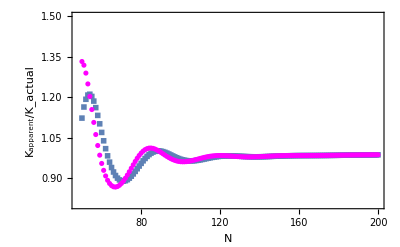

```mathematica
p1=ListPlot[PairsKratio,PlotMarkers-> ■ ,PlotRange->{{48,200},{0.8,1.5

}},AxesOrigin->{48,1.0},Frame->True,FrameTicks->True,FrameTicksStyle->Directive[18],FrameLabel->{Style["N",Italic,Large],Style["K_apparent/K_actual",Italic,Large],RotateLabel->True}];
p2=ListPlot[PairsKratioModel,PlotStyle->Magenta,PlotRange->All]; 
Show[p1,p2]
```